```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
Clear[LEFT]
```

```mathematica
Lead=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{{{0.-0.0000823223 ⅈ,-0.573223+0. ⅈ,0.+0.000025 ⅈ,0.25+0. ⅈ,0.-2.8033×10^-13 ⅈ,-0.0732233+0. ⅈ,0.-7.32233×10^-6 ⅈ,0.0732233+0. ⅈ,0.+0.0000146447 ⅈ,-0.176777+0. ⅈ,0.-0.0000323223 ⅈ,0.323223+0. ⅈ,0.+0.0000396447 ⅈ,-0.426777+0. ⅈ},12,{-0.426777+0. ⅈ,0.+1035.53 ⅈ,0.323223+0. ⅈ,8,0.+428.932 ⅈ,-0.46967+0. ⅈ,0.-1035.53 ⅈ}},299,{1}}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Lead[[ω*100+1]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
Clear[SR,SL]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:=Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

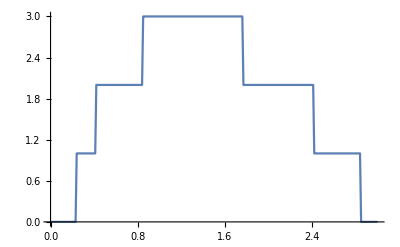

```mathematica
ListLinePlot[ParallelTable[{ω,tr[ω,0.0001,1,0]},{ω,Range[00,3,0.01]}]]
```

```mathematica
pris:=pris= Table[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,3,0.01]}]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentration]=Table[SortBy[Join[RandomSample[Join[s[1,100,1,7](*,s[38,50,38,50]*)],concentration],RandomSample[Join[s[1,100,8,14](*,s[38,50,1,37]*)],total-concentration]],First],1000]
```

```mathematica
f[ω_,δ_,t_,ϵ_,ϵ1_,unitcell_,total_,concentration_,number_]:=Inverse[Module[{J=β[ω,δ,t,ϵ],abc=dist[total,concentration][[number]]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]]
```

```mathematica
input[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_]:=Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{},
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-f[ω,δ,t,ϵ,ϵ1,unitcell,total,concentration,number].ConjugateTranspose[Tin].J.Tin].f[ω,δ,t,ϵ,ϵ1,unitcell,total,concentration,number],{unitcell,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];tra]
```

```mathematica
transmission100=Table[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[ξ]<>".dat"],{ξ,Range[1,190,2]}]
```

{{{0.,2.8×10^-7},{0.01,2.78688×10^-7},{0.02,2.81426×10^-7},{0.03,2.86149×10^-7},{0.04,2.91921×10^-7},{0.05,2.99702×10^-7},{0.06,3.104×10^-7},{0.07,3.236×10^-7},{0.08,3.39098×10^-7},283,{2.92,4.60063×10^-7},{2.93,3.54141×10^-7},{2.94,2.80823×10^-7},{2.95,2.27859×10^-7},{2.96,1.88758×10^-7},{2.97,1.58734×10^-7},{2.98,1.35435×10^-7},{2.99,1.16828×10^-7},{3.,1.02002×10^-7}},93,{1}}
 |  |  |  |

```mathematica
trans[n_]:=trans[n]= Monitor[Table[ParallelTable[{ω,input[ω,0.0001,1,0,0.5,n,(n-1)/2,number]},{ω,Range[0,3,0.01]}],{number,100}],number]
```

```mathematica
Clear[trans,misfit]
```

```mathematica
misfit[conc_,n_,x_,y_]:=Module[{m5=trans[conc][[n]]},
ρ1:= ParallelTable[{2ξ-1,Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-transmission100[[ξ]][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]},{ξ,95}]; 
ρ1]
```

```mathematica
errorconc[conc_,x_,y_]:=Mean[Table[Abs[(misfit[conc,n,x,y][[Position[misfit[conc,n,x,y],Min[misfit[conc,n,x,y]]][[1,1]]]][[1]]-conc)]/conc,{n,100}]]
```

```mathematica
Table[errorconc[conc,2.5,0],{conc,1,91,10}]
```

{0,8/275,1/30,73/1550,52/1025,21/425,157/3050,39/710,361/4050,232/2275}

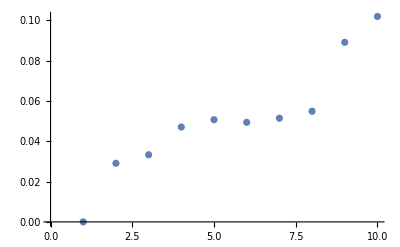

```mathematica
ListPlot[{0,8/275,1/30,73/1550,52/1025,21/425,157/3050,39/710,361/4050,232/2275}]
```

```mathematica
errorbw[x_,y_]:=Mean[Table[Abs[(misfit[n,x,y][[Position[misfit[n,x,y],Min[misfit[n,x,y]]][[1,1]]]][[1]]-49)]/49,{n,100}]]
```

```mathematica
Monitor[Table[{(x-0.5)/x,errorbw[x,0.5]//N},{x,Range[0.51,2.5,0.1]}],x]
```

{{0.0196078,0.786531},{0.180328,0.239592},{0.295775,0.135102},{0.382716,0.113878},{0.450549,0.111837},{0.50495,0.108571},{0.54955,0.112245},{0.586777,0.115918},{0.618321,0.0987755},{0.64539,0.0877551},{0.668874,0.0746939},{0.689441,0.0673469},{0.707602,0.0632653},{0.723757,0.06},{0.73822,0.0604082},{0.751244,0.0595918},{0.763033,0.0579592},{0.773756,0.055102},{0.78355,0.0522449},{0.792531,0.0514286}}

```mathematica
Export["~/PhD/invited/delta_error_bw.dat",%69]
```

~/PhD/invited/delta_error_bw.dat

```mathematica
Import["~/PhD/invited/delta_error_bw.dat"]
```

{{0.0196078,0.786531},{0.180328,0.239592},{0.295775,0.135102},{0.382716,0.113878},{0.450549,0.111837},{0.50495,0.108571},{0.54955,0.112245},{0.586777,0.115918},{0.618321,0.0987755},{0.64539,0.0877551},{0.668874,0.0746939},{0.689441,0.0673469},{0.707602,0.0632653},{0.723757,0.06},{0.73822,0.0604082},{0.751244,0.0595918},{0.763033,0.0579592},{0.773756,0.055102},{0.78355,0.0522449},{0.792531,0.0514286}}

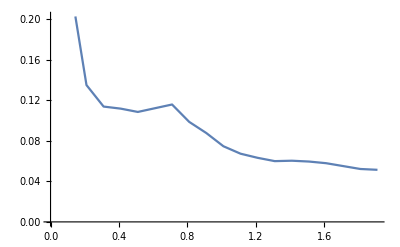

```mathematica
ListPlot[%51,Joined->True]
```

```mathematica
Interpolation[%51]
```

InterpolatingFunction[…]

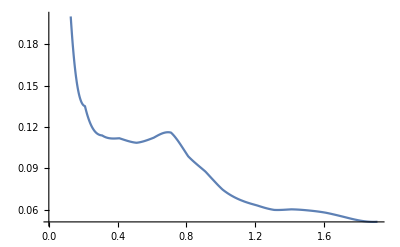

```mathematica
Plot[%60[x],{x,0.010000000000000009,1.9100000000000001}]
```

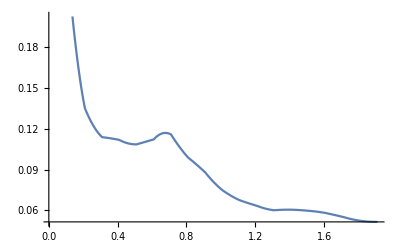

```mathematica
Plot[%58[x],{x,0.010000000000000009,1.9100000000000001}]
```

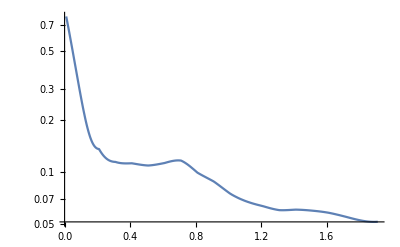

```mathematica
LogPlot[%53[x],{x,0.010000000000000009,1.9100000000000001},PlotRange->All]
```

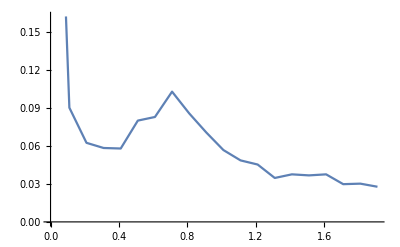

```mathematica
ListPlot[%48,Joined->True]
```